```mathematica
SetDirectory[NotebookDirectory[]];
```

## 4 loop running coupling

```mathematica
(* form hep-ph 9703284, vermaseren, larin, Ritbergen *)
ΛQCD=0.2145; 
(* so that for nF=5 we get alpha_s(mz=91.188)=0.1185 (PDG value) 
note that pdg also quotes λqcd=0.214 for nf=5 everything seems consistent*)

(*QCD*)
Nc=3.;CA=Nc; nF=3;
CF=(Nc^2-1)/(2 Nc);
(*coeft of the renormalization group equations*)
β0[Nf_]=(-11Nc+2Nf)/12;
β1[Nf_]=(-68 Nc^2+20Nc Nf+12CF Nf)/(3 32);
β2[Nf_]=-(2857-5033/9 Nf+325/27 Nf^2)/128; (*for Nc=3 only*)
β3[Nf_]=-1/256((149753/6+3564 Zeta[3])-(1078361/162+6508/27 Zeta[3])Nf+(50065/162+6472/81 Zeta[3])Nf^2+1093/729 Nf^3);(*for Nc=3 only*)

γ0[Nf_]=3/4 CF;
γ1[Nf_]=1/16(202/3-20/9 Nf);(*for Nc=3 only*)
γ2[Nf_]=1/64(1249+(-2216/27-160/3 Zeta[3])Nf-140/81 Nf^2);(*for Nc=3 only*)
γ3[Nf_]=1/256(4603055/162+135680/27 Zeta[3]-8800Zeta[5]+(-91723/27-34192/9 Zeta[3]+880 Zeta[4]+18400/9 Zeta[5])Nf+(5242/243+800/9 Zeta[3]-160/3 Zeta[4])Nf^2+(-332/243+64/27 Zeta[3])Nf^3);

b0[Nf_]=-(8β0[Nf])/(2(4π)^2);
b1[Nf_]=-(32 β1[Nf])/(2(4π)^2);

(* Initial conditions of the RG equations, μ in units of Λ_MSbar *)

(*gf[μ_]=1/√(2 b0 Log[μ]+b1 Log[2 Log[μ]]/b0);*)
gf[t_]=1/(√(b0[Nf] t+b1[Nf] Log[t]/b0[Nf]));
asf[t_,Nf_]=-1/(β0[Nf] t)-(β1[Nf] Log[t])/(β0[Nf]^3 t^2)-(β1[Nf]^2(Log[t]^2-Log[t]-1)+β2[Nf] β0[Nf])/(β0[Nf]^5 t^3)+1/(β0[Nf]^7 t^4)( β1[Nf]^3(-Log[t]^3+5/2 Log[t]^2+2Log[t]-1/2)-3 β1[Nf] β2[Nf] β0[Nf] Log[t]+1/2 β3[Nf] β0[Nf]^2);
μ0=2;
t0=Log[μ0^2];
tf=10000 t0;
(*solution of the RG equation to 3 loop*)
mcharm=1.275;(*m(m) in msbar*)
mbottom=4.18;
nf[t_]=If[t<Log[mcharm^2/ΛQCD^2],3,If[t<Log[mbottom^2/ΛQCD^2],4,5]];
sg4=Quiet[NDSolve[{D[as[t],t]==+β0[nf[t]] as[t]^2+β1[nf[t]] as[t]^3+ β2[nf[t]] as[t]^4+ β3[nf[t]] as[t]^5,as[tf]==asf[tf,nf[tf]]},as,{t,t0,tf},AccuracyGoal->14,WorkingPrecision->32,MaxSteps->10000000]];

a4t[t_]= Part[Evaluate[as[t]/.sg4],1];
g4[μ_]=2 π √Part[Evaluate[as[Log[μ^2/ΛQCD^2]]/.sg4],1];
```

## Generate Spectral Functions

```mathematica
R=20000;
Mc=1.4691897661033038;
Mb=4.882;
kfinal={0.6856700331366409,-0.31661256911352553};(*100k run*)
kfinalu={0.9065399936425322,-0.36858869824209667};
kfinall={0.4648000726307495,-0.2646364399849544};
αcont={0.5129548374487685,0.002435119807500435};(*10k run*)
σcont={0.16999653850906107,0.000838106749908169};
ccont={-0.1611740456186636,0.002474788649682089};
conv=0.197327;
ReVsbVac=8/10;
```

### Define required functions

```mathematica
ImVc1[r_,mD_,α_,T_]:=T α (1-1/2 √π MeijerG[{{0},{}},{{0,1},{-1/2}},(mD^2 r^2)/4]);
ImVc[r_,mD_,α_,T_]:=T α Quiet[2NIntegrate[z/((z^2+1)^2)(1-Sinc[mD r z]),{z,0,∞}]];
ReV[r_,m_,α_,σ_,c_]:=c-α m-α Exp[-m r]/r+(2 σ)/m-(ⅇ^(-m r) (2+m r) σ)/m;

ReVsb[r_,m_,α_,σ_,c_]:=If[ReV[r,m,α,σ,c]<ReVsbVac,ReV[r,m,α,σ,c],ReVsbVac];

ReVm0[r_,α_,σ_,c_]:=-α/r+σ r+c
```

```mathematica
mDcal[μ_,T_,c_,d_]:=Re[Sqrt[Nc/3+nF/6]g4[μ T]T+1/(4π)Nc g4[μ T]^2 T Log[Sqrt[Nc/3+nF/6]/g4[μ T]]+c g4[μ T]^2 T+d g4[μ T]^3 T ];
```

```mathematica
rsbvac=r/.FindRoot[ReVm0[r,αcont[[1]],σcont[[1]],ccont[[1]]]==8/10,{r,1}]
```

6.14511

### Plot potentials

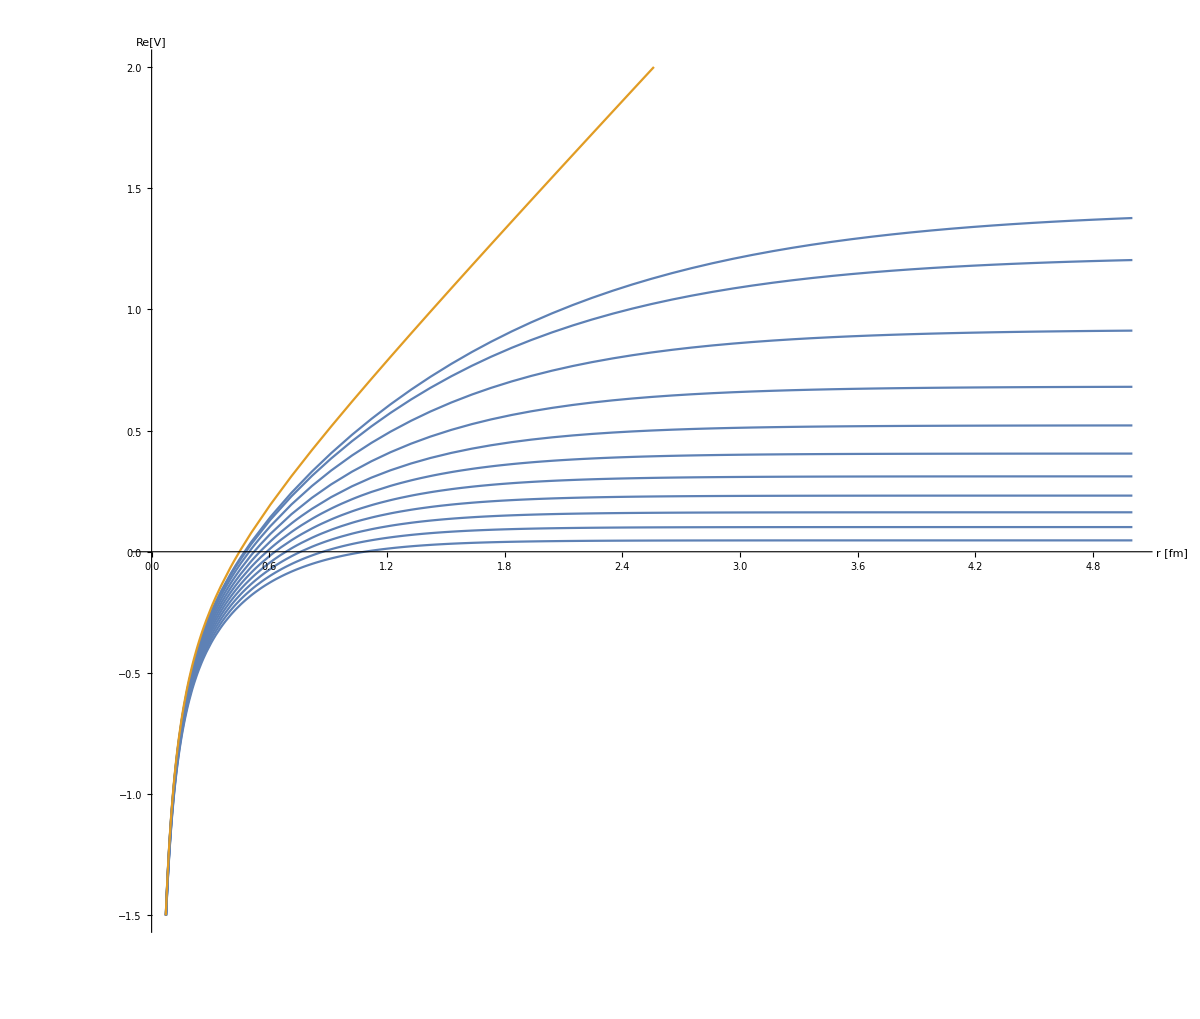

```mathematica
ReVplot=Table[ReV[r/0.197,mDcal[2π,Tscancorig[[5 l]],kfinal[[1]],kfinal[[2]]],αcont[[1]],σcont[[1]],ccont[[1]]],{l,Length[Tscancorig]/5}];
Plot[{ReVplot,ReVm0[r/0.197,αcont[[1]],σcont[[1]],ccont[[1]]]},{r,0,5},AxesStyle->Directive[FontSize->25,Thickness->0.004,FontFamily->"Helvetica",Black],BaseStyle->{FontSize->14},AspectRatio->0.85,AxesLabel->{"r [fm]","Re[V]"},ImageSize->{1200,1200},PlotRange->{-1.5,2},GridLines->{{conv rsbvac},{ReVsbVac}},GridLinesStyle->Directive[Gray, Dashed],BaseStyle->{FontSize->14}]
```

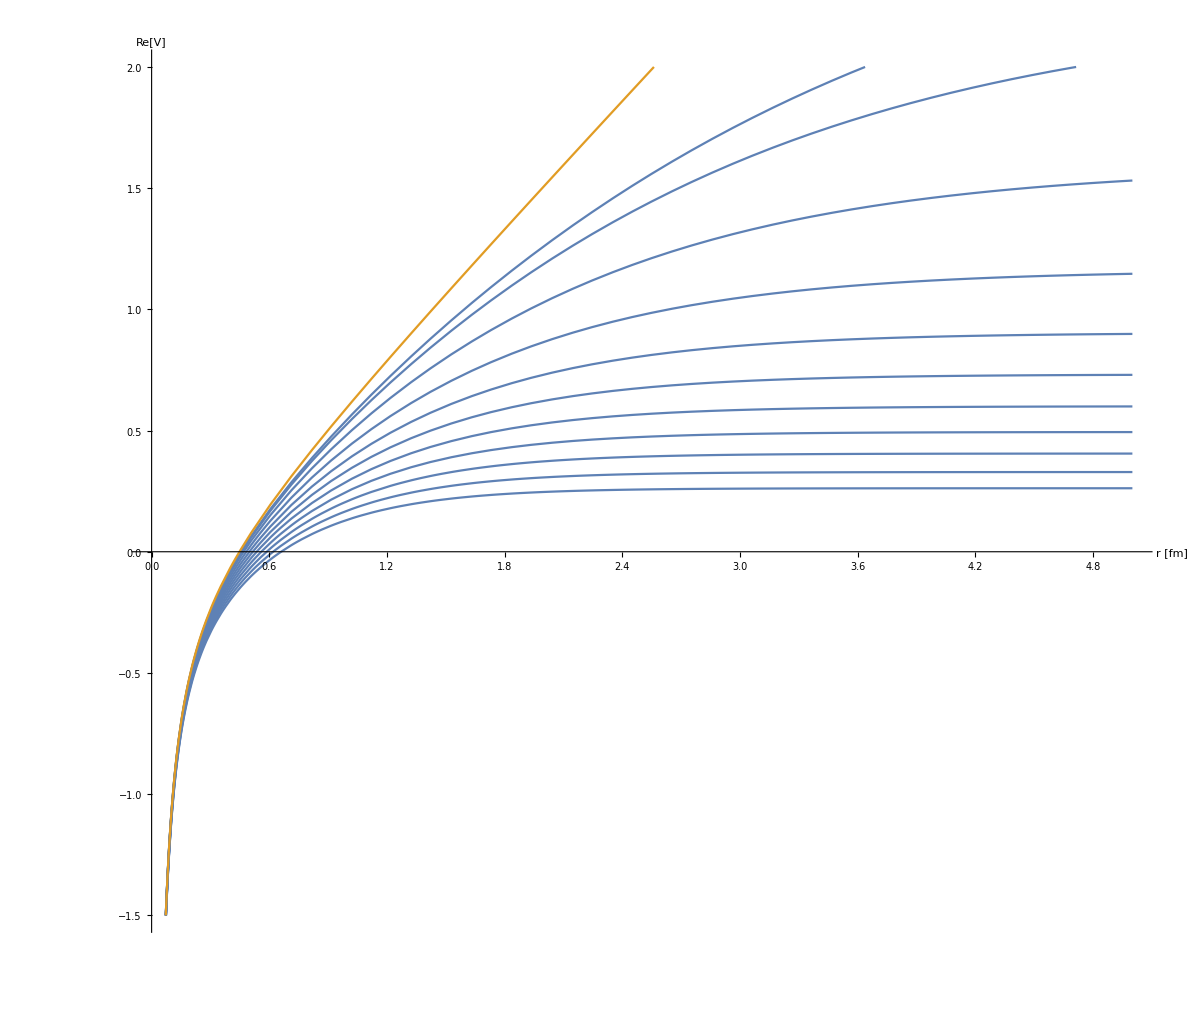

```mathematica
ReVplotl=Table[ReV[r/0.197,mDcal[2π,Tscancorig[[5 l]],kfinall[[1]],kfinall[[2]]],αcont[[1]],σcont[[1]],ccont[[1]]],{l,Length[Tscancorig]/5}];
Plot[{ReVplotl,ReVm0[r/0.197,αcont[[1]],σcont[[1]],ccont[[1]]]},{r,0,5},AxesStyle->Directive[FontSize->25,Thickness->0.004,FontFamily->"Helvetica",Black],BaseStyle->{FontSize->14},AspectRatio->0.85,AxesLabel->{"r [fm]","Re[V]"},ImageSize->{1200,1200},PlotRange->{-1.5,2},GridLines->{{conv rsbvac},{ReVsbVac}},GridLinesStyle->Directive[Gray, Dashed],BaseStyle->{FontSize->14}]
```

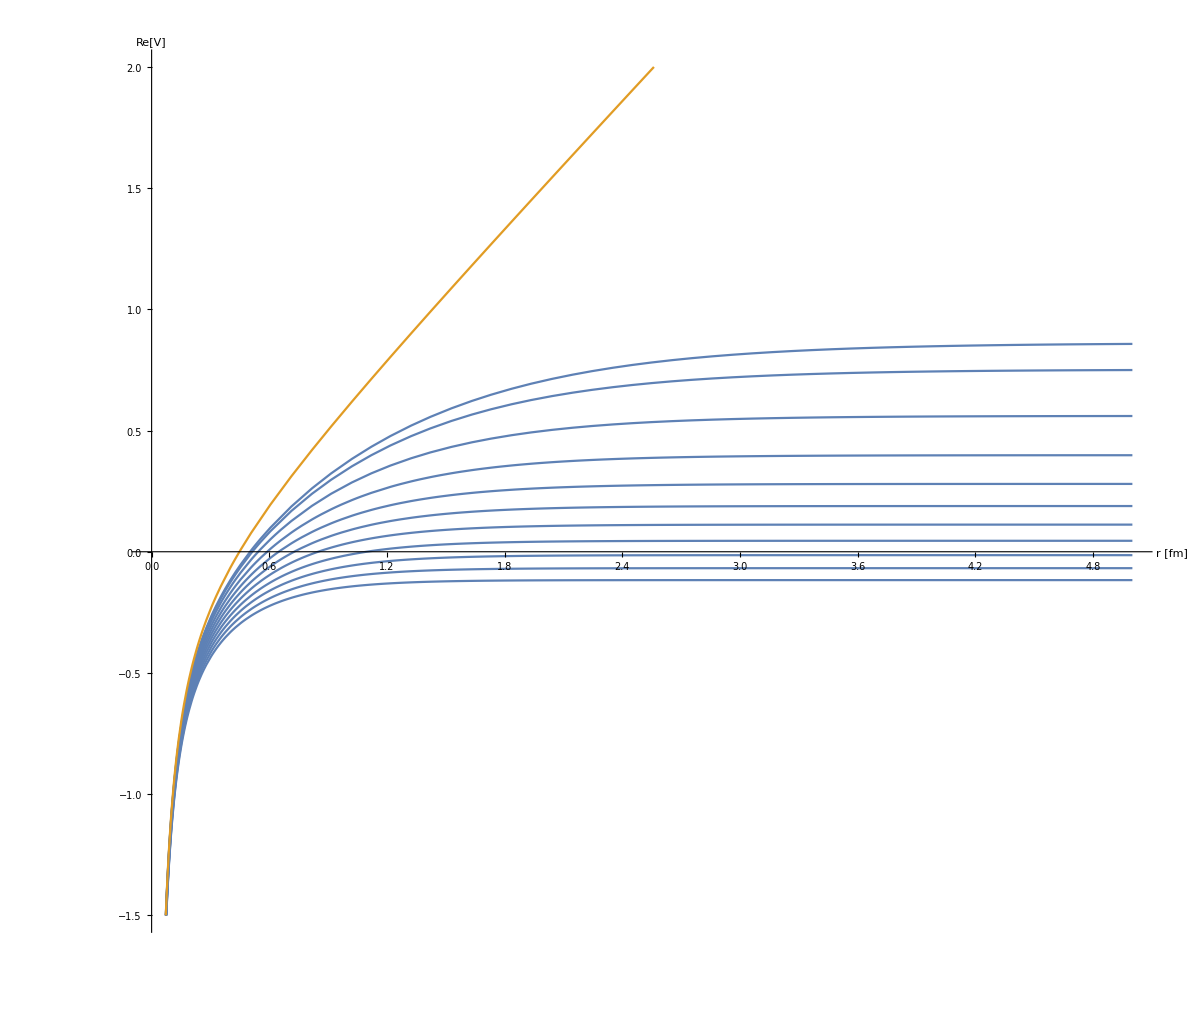

```mathematica
ReVplotu=Table[ReV[r/0.197,mDcal[2π,Tscancorig[[5 l]],kfinalu[[1]],kfinalu[[2]]],αcont[[1]],σcont[[1]],ccont[[1]]],{l,Length[Tscancorig]/5}];
Plot[{ReVplotu,ReVm0[r/0.197,αcont[[1]],σcont[[1]],ccont[[1]]]},{r,0,5},AxesStyle->Directive[FontSize->25,Thickness->0.004,FontFamily->"Helvetica",Black],BaseStyle->{FontSize->14},AspectRatio->0.85,AxesLabel->{"r [fm]","Re[V]"},ImageSize->{1200,1200},PlotRange->{-1.5,2},GridLines->{{conv rsbvac},{ReVsbVac}},GridLinesStyle->Directive[Gray, Dashed],BaseStyle->{FontSize->14}]
```

### Regularisation

```mathematica
Tscancorig=Join[Table[i,{i,0.15,0.16,0.001}],Table[i,{i,0.162,0.3,0.003}]]
```

{0.15,0.151,0.152,0.153,0.154,0.155,0.156,0.157,0.158,0.159,0.16,0.162,0.165,0.168,0.171,0.174,0.177,0.18,0.183,0.186,0.189,0.192,0.195,0.198,0.201,0.204,0.207,0.21,0.213,0.216,0.219,0.222,0.225,0.228,0.231,0.234,0.237,0.24,0.243,0.246,0.249,0.252,0.255,0.258,0.261,0.264,0.267,0.27,0.273,0.276,0.279,0.282,0.285,0.288,0.291,0.294,0.297,0.3}

```mathematica
Tscanborig=Table[i,{i,0.15,0.6,0.005}]
```

{0.15,0.155,0.16,0.165,0.17,0.175,0.18,0.185,0.19,0.195,0.2,0.205,0.21,0.215,0.22,0.225,0.23,0.235,0.24,0.245,0.25,0.255,0.26,0.265,0.27,0.275,0.28,0.285,0.29,0.295,0.3,0.305,0.31,0.315,0.32,0.325,0.33,0.335,0.34,0.345,0.35,0.355,0.36,0.365,0.37,0.375,0.38,0.385,0.39,0.395,0.4,0.405,0.41,0.415,0.42,0.425,0.43,0.435,0.44,0.445,0.45,0.455,0.46,0.465,0.47,0.475,0.48,0.485,0.49,0.495,0.5,0.505,0.51,0.515,0.52,0.525,0.53,0.535,0.54,0.545,0.55,0.555,0.56,0.565,0.57,0.575,0.58,0.585,0.59,0.595,0.6}

```mathematica
ImVsTab[mD1_,Δ1_,σ1_,T1_]:=Block[{mD=mD1,Δ=Δ1,σ=σ1,T=T1},Join[{{0,0}},ParallelTable[{r,NIntegrate[(2 mD^2 T σ (2-2 Cos[p r]-p r Sin[p r]))/((mD^2+p^2)^2 √(p^2+Δ^2)),{p,0,∞},MaxRecursion->20]},{r,1/100,200,1/100}]]];
ImVsAs[mD_,Δ_,σ_,T_]:=4 mD^2 T σ NIntegrate[1/((mD^2+p^2)^2 √(p^2+Δ^2)),{p,0,∞},WorkingPrecision->20,MaxRecursion->20];
ImVsr[r_,mD_,Δ_,σ_,T_]:=2 mD^2 T σ NIntegrate[(2-2 Cos[p r]-p r Sin[p r])/((mD^2+p^2)^2 √(p^2+Δ^2)),{p,0,∞},WorkingPrecision->20,MaxRecursion->20];
```

```mathematica
ImVsAsN[Δmd_]:= NIntegrate[4/((1+p^2)^2 √(p^2+Δmd^2)),{p,0,∞},WorkingPrecision->20,MaxRecursion->20];
```

```mathematica
reg=3;
While[ImVsAsN[reg]>1,reg=reg+1/100000];
```

```mathematica
reg=303689/100000;
```

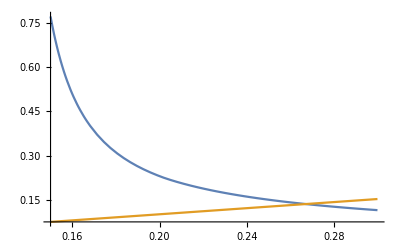

```mathematica
Plot[{(σcont[[1]]T)/mDcal[2π,T,kfinal[[1]],kfinal[[2]]]^2,αcont[[1]]T},{T,0.15,0.3},PlotRange->All ]
```

```mathematica
Block[{n=1},Quiet[mDcal[2π,Tscancorig[[n]],kfinal[[1]],kfinal[[2]]]^2/(σcont[[1]] Tscancorig[[n]])ImVsr[10000,mDcal[2π,Tscancorig[[n]],kfinal[[1]],kfinal[[2]]],reg mDcal[2π,Tscancorig[[n]],kfinal[[1]],kfinal[[2]]],σcont[[1]],Tscancorig[[n]]]]]
```

0.999998

```mathematica
Tscandiff={0.17,0.175,0.185,0.19,0.2,0.205,0.215,0.22,0.23,0.235,0.245,0.25,0.26,0.265,0.275,0.28,0.29,0.295};
```

```mathematica
ImVsAll[n1_]:=Block[{n=n1,temp},temp=ImVsTab[mDcal[2π,Tscandiff[[n]],kfinal[[1]],kfinal[[2]]],reg mDcal[2π,Tscandiff[[n]],kfinal[[1]],kfinal[[2]]],σcont[[1]],Tscandiff[[n]]];
Export["pots/ImVsT"<>ToString[Round[1000 Tscandiff[[n]]]]<>".dat",temp];]
```

```mathematica
ImVsuAll[n1_]:=Block[{n=n1,temp},temp=ImVsTab[mDcal[2π,Tscandiff[[n]],kfinalu[[1]],kfinalu[[2]]],reg mDcal[2π,Tscandiff[[n]],kfinalu[[1]],kfinalu[[2]]],σcont[[1]],Tscandiff[[n]]];
Export["pots/ImVsuT"<>ToString[Round[1000 Tscandiff[[n]]]]<>".dat",temp];]
```

```mathematica
ImVslAll[n1_]:=Block[{n=n1,temp},temp=ImVsTab[mDcal[2π,Tscanborig[[n]],kfinall[[1]],kfinall[[2]]],reg mDcal[2π,Tscanborig[[n]],kfinall[[1]],kfinall[[2]]],σcont[[1]],Tscanborig[[n]]];
Export["pots/ImVslT"<>ToString[Round[1000 Tscanborig[[n]]]]<>".dat",temp];]
```

```mathematica
Do[ImVsAll[n],{n,Length[Tscandiff]}]
```

```mathematica
Do[ImVsuAll[n],{n,Length[Tscandiff]}]
```

```mathematica
Do[ImVslAll[n],{n,Length[Tscandiff]}]
```

```mathematica
Block[{data},Do[data=ToExpression[Import["pots/ImVsT"<>ToString[Round[1000Tscancorig[[n]]]]<>".dat"]];data=Append[data,{20000,data[[-1,2]]}];ImVsregInter[n]=Interpolation[data,InterpolationOrder->1],{n,Length[Tscancorig]}]];
```

```mathematica
Block[{data},Do[data=ToExpression[Import["pots/ImVslT"<>ToString[Round[1000Tscancorig[[n]]]]<>".dat"]];data=Append[data,{20000,data[[-1,2]]}];ImVsreglInter[n]=Interpolation[data,InterpolationOrder->1],{n,Length[Tscancorig]}]];
```

```mathematica
Block[{data},Do[data=ToExpression[Import["pots/ImVsuT"<>ToString[Round[1000Tscancorig[[n]]]]<>".dat"]];data=Append[data,{20000,data[[-1,2]]}];ImVsreguInter[n]=Interpolation[data,InterpolationOrder->1],{n,Length[Tscancorig]}]];
```

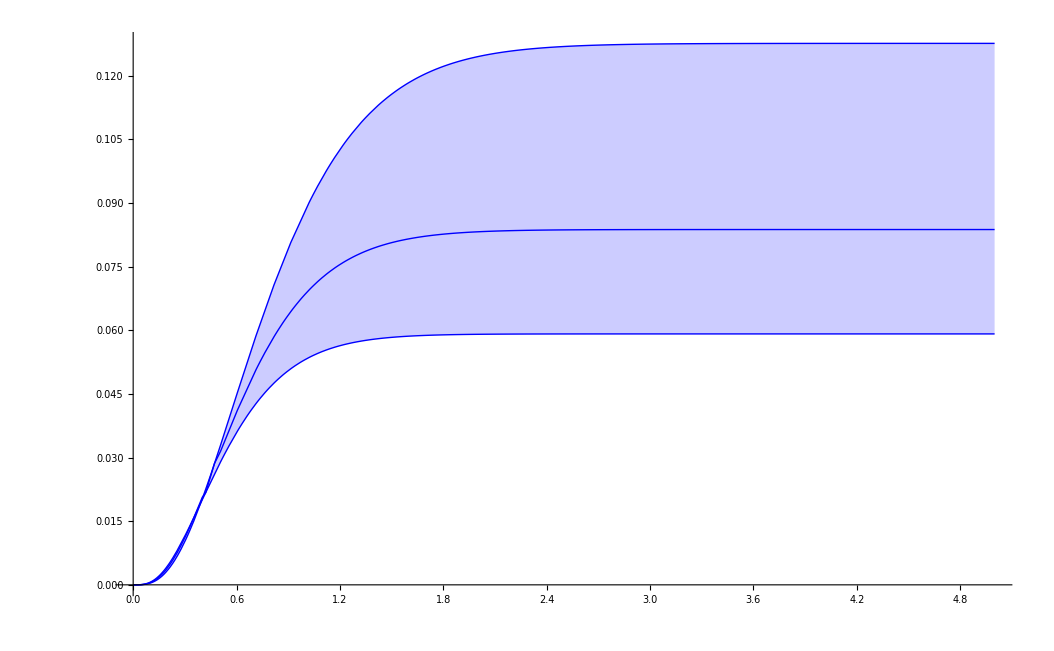

```mathematica
Block[{n=50},Plot[{ImVsregInter[n][x/conv],ImVsreguInter[n][x/conv],ImVsreglInter[n][x/conv]},{x,0,5},PlotStyle->{{Blue,Thick},{Blue,Thin},{Blue,Thin}},Filling->{1->{2},1->{3}}]]
```

### Modules

```mathematica
ParallelSow[expr_]:=Sow[expr];
SetSharedFunction[ParallelSow];
```

```mathematica
δ=1/100; 
dω=0.0002;
```

#### Charmonium s - wave

```mathematica
swaveccspectra[n_,Tscan_]:=Block[{T=Tscan[[n]],mD=mDcal[2π,Tscan[[n]],kfinal[[1]],kfinal[[2]]],σ=σcont[[1]],α=αcont[[1]],c=ccont[[1]],M=Mc,l=0,ωmin=-1,ωmax=2,inf,ρtable,ω,rhow,gr0,s1,s01,rev,imvc,V,ccsT},

rev=Interpolation[Join[ParallelTable[{r,ReVsb[r,mD,α,σ,c]},{r,1/1000,10,1/100}],ParallelTable[{r,ReVsb[r,mD,α,σ,c]},{r,101/10,25,1/10}],ParallelTable[{r,ReVsb[r,mD,α,σ,c]},{r,26,1500,1}],ParallelTable[{r,ReVsb[r,mD,α,σ,c]},{r,1510,20000,1000}]]];
imvc=Interpolation[Join[ParallelTable[{r,ImVc[r,mD,α,T]},{r,1/1000,10,1/100}],ParallelTable[{r,ImVc[r,mD,α,T]},{r,101/10,25,1/10}],ParallelTable[{r,ImVc[r,mD,α,T]},{r,26,1500,1}],ParallelTable[{r,ImVc[r,mD,α,T]},{r,1510,20000,1000}]]];
V[x_]:=rev[x]+ⅈ (imvc[x]+ImVsregInter[n][x]);

ρtable=ParallelDo[ω=ωmin+(it-1) dω M;inf=40+500*it*dω;
s01=NDSolve[{(ω-(l(l+1))/(M r^2)-Re[V[r]]+ⅈ Abs[Im[V[r]]])gr[r]+1/M gr''[r]==0, 
gr'[δ]==(α M)-δ(M α)^2,
 gr[δ]==δ(α M)- 1/2 δ^2(α M)^2},gr,{r,δ,inf}];
gr0[r_]=(gr[r]/.s01)_⟦1⟧;
s1=NDSolve[{rho'[x]==-(6 Nc M^2 α)/(4π)Im[1/(gr0[x])^2],rho[δ]==0},rho,{x,δ,inf}];
rhow[r_]=(rho[r]/.s1)_⟦1⟧;
ParallelSow[{ω+2M,rhow[inf]}],{it,1,(ωmax-ωmin)/(dω M)}]//Reap//Last//First;

ccsT=ParallelTable[{ρtable[[i,1]],ρtable[[i,2]]/ρtable[[i,1]]^2},{i,1,Length[ρtable]}];
Export["cc/swccT"<>ToString[Round[T*1000]]<>"spectra.dat",Sort[ccsT]];
];
```

```mathematica
swavecclspectra[n_,Tscan_]:=Block[{T=Tscan[[n]],mD=mDcal[2π,Tscan[[n]],kfinall[[1]],kfinall[[2]]],σ=σcont[[1]],α=αcont[[1]],c=ccont[[1]],M=Mc,l=0,ωmin=-1,ωmax=2,inf,ρtable,ω,rhow,gr0,s1,s01,rev,imvc,V,ccsT},

rev=Interpolation[Join[ParallelTable[{r,ReVsb[r,mD,α,σ,c]},{r,1/1000,10,1/100}],ParallelTable[{r,ReVsb[r,mD,α,σ,c]},{r,101/10,25,1/10}],ParallelTable[{r,ReVsb[r,mD,α,σ,c]},{r,26,1500,1}],ParallelTable[{r,ReVsb[r,mD,α,σ,c]},{r,1510,20000,1000}]]];
imvc=Interpolation[Join[ParallelTable[{r,ImVc[r,mD,α,T]},{r,1/1000,10,1/100}],ParallelTable[{r,ImVc[r,mD,α,T]},{r,101/10,25,1/10}],ParallelTable[{r,ImVc[r,mD,α,T]},{r,26,1500,1}],ParallelTable[{r,ImVc[r,mD,α,T]},{r,1510,20000,1000}]]];
V[x_]:=rev[x]+ⅈ (imvc[x]+ImVsreglInter[n][x]);

ρtable=ParallelDo[ω=ωmin+(it-1) dω M;inf=40+500*it*dω;
s01=NDSolve[{(ω-(l(l+1))/(M r^2)-Re[V[r]]+ⅈ Abs[Im[V[r]]])gr[r]+1/M gr''[r]==0, 
gr'[δ]==(α M)-δ(M α)^2,
 gr[δ]==δ(α M)- 1/2 δ^2(α M)^2},gr,{r,δ,inf}];
gr0[r_]=(gr[r]/.s01)_⟦1⟧;
s1=NDSolve[{rho'[x]==-(6 Nc M^2 α)/(4π)Im[1/(gr0[x])^2],rho[δ]==0},rho,{x,δ,inf}];
rhow[r_]=(rho[r]/.s1)_⟦1⟧;
ParallelSow[{ω+2M,rhow[inf]}],{it,1,(ωmax-ωmin)/(dω M)}]//Reap//Last//First;

ccsT=ParallelTable[{ρtable[[i,1]],ρtable[[i,2]]/ρtable[[i,1]]^2},{i,1,Length[ρtable]}];
Export["cc/swccT"<>ToString[Round[T*1000]]<>"lspectra.dat",Sort[ccsT]];
];
```

```mathematica
swaveccuspectra[n_,Tscan_]:=Block[{T=Tscan[[n]],mD=mDcal[2π,Tscan[[n]],kfinalu[[1]],kfinalu[[2]]],σ=σcont[[1]],α=αcont[[1]],c=ccont[[1]],M=Mc,l=0,ωmin=-1,ωmax=2,inf,ρtable,ω,rhow,gr0,s1,s01,rev,imvc,V,ccsT},

rev=Interpolation[Join[ParallelTable[{r,ReVsb[r,mD,α,σ,c]},{r,1/1000,10,1/100}],ParallelTable[{r,ReVsb[r,mD,α,σ,c]},{r,101/10,25,1/10}],ParallelTable[{r,ReVsb[r,mD,α,σ,c]},{r,26,1500,1}],ParallelTable[{r,ReVsb[r,mD,α,σ,c]},{r,1510,20000,1000}]]];
imvc=Interpolation[Join[ParallelTable[{r,ImVc[r,mD,α,T]},{r,1/1000,10,1/100}],ParallelTable[{r,ImVc[r,mD,α,T]},{r,101/10,25,1/10}],ParallelTable[{r,ImVc[r,mD,α,T]},{r,26,1500,1}],ParallelTable[{r,ImVc[r,mD,α,T]},{r,1510,20000,1000}]]];
V[x_]:=rev[x]+ⅈ (imvc[x]+ImVsreguInter[n][x]);

ρtable=ParallelDo[ω=ωmin+(it-1) dω M;inf=40+500*it*dω;
s01=NDSolve[{(ω-(l(l+1))/(M r^2)-Re[V[r]]+ⅈ Abs[Im[V[r]]])gr[r]+1/M gr''[r]==0, 
gr'[δ]==(α M)-δ(M α)^2,
 gr[δ]==δ(α M)- 1/2 δ^2(α M)^2},gr,{r,δ,inf}];
gr0[r_]=(gr[r]/.s01)_⟦1⟧;
s1=NDSolve[{rho'[x]==-(6 Nc M^2 α)/(4π)Im[1/(gr0[x])^2],rho[δ]==0},rho,{x,δ,inf}];
rhow[r_]=(rho[r]/.s1)_⟦1⟧;
ParallelSow[{ω+2M,rhow[inf]}],{it,1,(ωmax-ωmin)/(dω M)}]//Reap//Last//First;

ccsT=ParallelTable[{ρtable[[i,1]],ρtable[[i,2]]/ρtable[[i,1]]^2},{i,1,Length[ρtable]}];
Export["cc/swccT"<>ToString[Round[T*1000]]<>"uspectra.dat",Sort[ccsT]];
];
```

#### Charmonium p - wave

```mathematica
pwaveccspectra[n_,Tscan_]:=Block[{T=Tscan[[n]],mD=mDcal[2π,Tscan[[n]],kfinal[[1]],kfinal[[2]]],σ=σcont[[1]],α=αcont[[1]],c=ccont[[1]],M=Mc,l=1,ωmin=-1,ωmax=2,ccsT,Tstring,inf,rev,imvc,V,ρtable,ω,s0,gr,gr1,s01,gr0,s1,rhow},

rev=Interpolation[Join[ParallelTable[{r,ReVsb[r,mD,α,σ,c]},{r,1/1000,10,1/100}],ParallelTable[{r,ReVsb[r,mD,α,σ,c]},{r,101/10,25,1/10}],ParallelTable[{r,ReVsb[r,mD,α,σ,c]},{r,26,1500,1}],ParallelTable[{r,ReVsb[r,mD,α,σ,c]},{r,1510,20000,1000}]]];
imvc=Interpolation[Join[ParallelTable[{r,ImVc[r,mD,α,T]},{r,1/1000,10,1/100}],ParallelTable[{r,ImVc[r,mD,α,T]},{r,101/10,25,1/10}],ParallelTable[{r,ImVc[r,mD,α,T]},{r,26,1500,1}],ParallelTable[{r,ImVc[r,mD,α,T]},{r,1510,20000,1000}]]];
V[x_]:=rev[x]+ⅈ (imvc[x]+ImVsregInter[n][x]);

ρtable=ParallelDo[ω=ωmin+(it-1) dω M;inf=40+500*it*dω;
s0=NDSolve[{(ω-(l(l+1))/(M r^2)-Re[V[r]]+ⅈ Abs[Im[V[r]]])gr[r]+1/M gr''[r]==0, 
gr'[δ]==2 δ(α M)^2-3/4 δ^2(M α)^3,
 gr[δ]== δ^2(α M)^2-1/4 δ^3(M α)^3},gr,{r,δ,inf},PrecisionGoal->10,MaxSteps->1000000];
gr1[r_]=(gr[r]/.s0)_⟦1⟧;
s01=NDSolve[{(ω-(l(l+1))/(M r^2)-Re[V[r]]+ⅈ Abs[Im[V[r]]])gr[r]+1/M gr''[r]==0, 
gr'[δ]==(α M)-δ(M α)^2,
 gr[δ]==δ(α M)- 1/2 δ^2(α M)^2},gr,{r,δ,inf}];
gr0[r_]=(gr[r]/.s01)_⟦1⟧;
s1=NDSolve[{rho'[x]==(Nc M^2 α^3)/(8π)Im[1/(gr0[x])^2+36/(gr1[x])^2],rho[δ]==0},rho,{x,δ,inf}];
rhow[r_]=(rho[r]/.s1)_⟦1⟧;
ParallelSow[{ω+2M,rhow[inf]}],{it,1,(ωmax-ωmin)/(dω M)}]//Reap//Last//First;

ccsT=ParallelTable[{ρtable[[i,1]],ρtable[[i,2]]/ρtable[[i,1]]^2},{i,1,Length[ρtable]}];
Tstring=Round[T*1000];
Export["cc/pwccT"<>ToString[Tstring]<>"spectra.dat",Sort[ccsT]];
];
```

```mathematica
pwaveccuspectra[n_,Tscan_]:=Block[{T=Tscan[[n]],mD=mDcal[2π,Tscan[[n]],kfinalu[[1]],kfinalu[[2]]],σ=σcont[[1]],α=αcont[[1]],c=ccont[[1]],M=Mc,l=1,ωmin=-1,ωmax=2,ccsT,Tstring,inf,rev,imvc,V,ρtable,ω,s0,gr,gr1,s01,gr0,s1,rhow},

rev=Interpolation[Join[ParallelTable[{r,ReVsb[r,mD,α,σ,c]},{r,1/1000,10,1/100}],ParallelTable[{r,ReVsb[r,mD,α,σ,c]},{r,101/10,25,1/10}],ParallelTable[{r,ReVsb[r,mD,α,σ,c]},{r,26,1500,1}],ParallelTable[{r,ReVsb[r,mD,α,σ,c]},{r,1510,20000,1000}]]];
imvc=Interpolation[Join[ParallelTable[{r,ImVc[r,mD,α,T]},{r,1/1000,10,1/100}],ParallelTable[{r,ImVc[r,mD,α,T]},{r,101/10,25,1/10}],ParallelTable[{r,ImVc[r,mD,α,T]},{r,26,1500,1}],ParallelTable[{r,ImVc[r,mD,α,T]},{r,1510,20000,1000}]]];
V[x_]:=rev[x]+ⅈ (imvc[x]+ImVsreguInter[n][x]);

ρtable=ParallelDo[ω=ωmin+(it-1) dω M;inf=40+500*it*dω;
s0=NDSolve[{(ω-(l(l+1))/(M r^2)-Re[V[r]]+ⅈ Abs[Im[V[r]]])gr[r]+1/M gr''[r]==0, 
gr'[δ]==2 δ(α M)^2-3/4 δ^2(M α)^3,
 gr[δ]== δ^2(α M)^2-1/4 δ^3(M α)^3},gr,{r,δ,inf},PrecisionGoal->10,MaxSteps->1000000];
gr1[r_]=(gr[r]/.s0)_⟦1⟧;
s01=NDSolve[{(ω-(l(l+1))/(M r^2)-Re[V[r]]+ⅈ Abs[Im[V[r]]])gr[r]+1/M gr''[r]==0, 
gr'[δ]==(α M)-δ(M α)^2,
 gr[δ]==δ(α M)- 1/2 δ^2(α M)^2},gr,{r,δ,inf}];
gr0[r_]=(gr[r]/.s01)_⟦1⟧;
s1=NDSolve[{rho'[x]==(Nc M^2 α^3)/(8π)Im[1/(gr0[x])^2+36/(gr1[x])^2],rho[δ]==0},rho,{x,δ,inf}];
rhow[r_]=(rho[r]/.s1)_⟦1⟧;
ParallelSow[{ω+2M,rhow[inf]}],{it,1,(ωmax-ωmin)/(dω M)}]//Reap//Last//First;

ccsT=ParallelTable[{ρtable[[i,1]],ρtable[[i,2]]/ρtable[[i,1]]^2},{i,1,Length[ρtable]}];
Tstring=Round[T*1000];
Export["cc/pwccT"<>ToString[Tstring]<>"uspectra.dat",Sort[ccsT]];
];
```

```mathematica
pwavecclspectra[n_,Tscan_]:=Block[{T=Tscan[[n]],mD=mDcal[2π,Tscan[[n]],kfinall[[1]],kfinall[[2]]],σ=σcont[[1]],α=αcont[[1]],c=ccont[[1]],M=Mc,l=1,ωmin=-1,ωmax=2,ccsT,Tstring,inf,rev,imvc,V,ρtable,ω,s0,gr,gr1,s01,gr0,s1,rhow},

rev=Interpolation[Join[ParallelTable[{r,ReVsb[r,mD,α,σ,c]},{r,1/1000,10,1/100}],ParallelTable[{r,ReVsb[r,mD,α,σ,c]},{r,101/10,25,1/10}],ParallelTable[{r,ReVsb[r,mD,α,σ,c]},{r,26,1500,1}],ParallelTable[{r,ReVsb[r,mD,α,σ,c]},{r,1510,20000,1000}]]];
imvc=Interpolation[Join[ParallelTable[{r,ImVc[r,mD,α,T]},{r,1/1000,10,1/100}],ParallelTable[{r,ImVc[r,mD,α,T]},{r,101/10,25,1/10}],ParallelTable[{r,ImVc[r,mD,α,T]},{r,26,1500,1}],ParallelTable[{r,ImVc[r,mD,α,T]},{r,1510,20000,1000}]]];
V[x_]:=rev[x]+ⅈ (imvc[x]+ImVsreglInter[n][x]);

ρtable=ParallelDo[ω=ωmin+(it-1) dω M;inf=40+500*it*dω;
s0=NDSolve[{(ω-(l(l+1))/(M r^2)-Re[V[r]]+ⅈ Abs[Im[V[r]]])gr[r]+1/M gr''[r]==0, 
gr'[δ]==2 δ(α M)^2-3/4 δ^2(M α)^3,
 gr[δ]== δ^2(α M)^2-1/4 δ^3(M α)^3},gr,{r,δ,inf},PrecisionGoal->10,MaxSteps->1000000];
gr1[r_]=(gr[r]/.s0)_⟦1⟧;
s01=NDSolve[{(ω-(l(l+1))/(M r^2)-Re[V[r]]+ⅈ Abs[Im[V[r]]])gr[r]+1/M gr''[r]==0, 
gr'[δ]==(α M)-δ(M α)^2,
 gr[δ]==δ(α M)- 1/2 δ^2(α M)^2},gr,{r,δ,inf}];
gr0[r_]=(gr[r]/.s01)_⟦1⟧;
s1=NDSolve[{rho'[x]==(Nc M^2 α^3)/(8π)Im[1/(gr0[x])^2+36/(gr1[x])^2],rho[δ]==0},rho,{x,δ,inf}];
rhow[r_]=(rho[r]/.s1)_⟦1⟧;
ParallelSow[{ω+2M,rhow[inf]}],{it,1,(ωmax-ωmin)/(dω M)}]//Reap//Last//First;

ccsT=ParallelTable[{ρtable[[i,1]],ρtable[[i,2]]/ρtable[[i,1]]^2},{i,1,Length[ρtable]}];
Tstring=Round[T*1000];
Export["cc/pwccT"<>ToString[Tstring]<>"lspectra.dat",Sort[ccsT]];
];
```

#### Bottomonium s - wave

```mathematica
swavebbspectra[n_,Tscan_]:=Block[{T=Tscan[[n]],mD=mDcal[2π,Tscan[[n]],kfinal[[1]],kfinal[[2]]],σ=σcont[[1]],α=αcont[[1]],c=ccont[[1]],M=Mb,l=0,ωmin=-1,ωmax=3,inf,ρtable,ω,rhow,gr0,s1,s01,rev,imvc,V,bbsT},

rev=Interpolation[Join[ParallelTable[{r,ReVsb[r,mD,α,σ,c]},{r,1/1000,10,1/100}],ParallelTable[{r,ReVsb[r,mD,α,σ,c]},{r,101/10,25,1/10}],ParallelTable[{r,ReVsb[r,mD,α,σ,c]},{r,26,1500,1}],ParallelTable[{r,ReVsb[r,mD,α,σ,c]},{r,1510,20000,1000}]]];
imvc=Interpolation[Join[ParallelTable[{r,ImVc[r,mD,α,T]},{r,1/1000,10,1/100}],ParallelTable[{r,ImVc[r,mD,α,T]},{r,101/10,25,1/10}],ParallelTable[{r,ImVc[r,mD,α,T]},{r,26,1500,1}],ParallelTable[{r,ImVc[r,mD,α,T]},{r,1510,20000,1000}]]];
V[x_]:=rev[x]+ⅈ (imvc[x]+ImVsregInter[n][x]);

ρtable=ParallelDo[ω=ωmin+(it-1) dω M;inf=40+500*it*dω;
s01=NDSolve[{(ω-(l(l+1))/(M r^2)-Re[V[r]]+ⅈ Abs[Im[V[r]]])gr[r]+1/M gr''[r]==0, 
gr'[δ]==(α M)-δ(M α)^2,
 gr[δ]==δ(α M)- 1/2 δ^2(α M)^2},gr,{r,δ,inf}];
gr0[r_]=(gr[r]/.s01)_⟦1⟧;
s1=NDSolve[{rho'[x]==-(6 Nc M^2 α)/(4π)Im[1/(gr0[x])^2],rho[δ]==0},rho,{x,δ,inf}];
rhow[r_]=(rho[r]/.s1)_⟦1⟧;
ParallelSow[{ω+2M,rhow[inf]}],{it,1,(ωmax-ωmin)/(dω M)}]//Reap//Last//First;

bbsT=ParallelTable[{ρtable[[i,1]],ρtable[[i,2]]/ρtable[[i,1]]^2},{i,1,Length[ρtable]}];
Export["bb/swbbT"<>ToString[Round[T*1000]]<>"spectra.dat",Sort[bbsT]];
];
```

```mathematica
swavebblspectra[n_,Tscan_]:=Block[{T=Tscan[[n]],mD=mDcal[2π,Tscan[[n]],kfinall[[1]],kfinall[[2]]],σ=σcont[[1]],α=αcont[[1]],c=ccont[[1]],M=Mb,l=0,ωmin=-1,ωmax=3,inf,ρtable,ω,rhow,gr0,s1,s01,rev,imvc,V,bbsT},

rev=Interpolation[Join[ParallelTable[{r,ReVsb[r,mD,α,σ,c]},{r,1/1000,10,1/100}],ParallelTable[{r,ReVsb[r,mD,α,σ,c]},{r,101/10,25,1/10}],ParallelTable[{r,ReVsb[r,mD,α,σ,c]},{r,26,1500,1}],ParallelTable[{r,ReVsb[r,mD,α,σ,c]},{r,1510,20000,1000}]]];
imvc=Interpolation[Join[ParallelTable[{r,ImVc[r,mD,α,T]},{r,1/1000,10,1/100}],ParallelTable[{r,ImVc[r,mD,α,T]},{r,101/10,25,1/10}],ParallelTable[{r,ImVc[r,mD,α,T]},{r,26,1500,1}],ParallelTable[{r,ImVc[r,mD,α,T]},{r,1510,20000,1000}]]];
V[x_]:=rev[x]+ⅈ (imvc[x]+ImVsreglInter[n][x]);

ρtable=ParallelDo[ω=ωmin+(it-1) dω M;inf=40+500*it*dω;
s01=NDSolve[{(ω-(l(l+1))/(M r^2)-Re[V[r]]+ⅈ Abs[Im[V[r]]])gr[r]+1/M gr''[r]==0, 
gr'[δ]==(α M)-δ(M α)^2,
 gr[δ]==δ(α M)- 1/2 δ^2(α M)^2},gr,{r,δ,inf}];
gr0[r_]=(gr[r]/.s01)_⟦1⟧;
s1=NDSolve[{rho'[x]==-(6 Nc M^2 α)/(4π)Im[1/(gr0[x])^2],rho[δ]==0},rho,{x,δ,inf}];
rhow[r_]=(rho[r]/.s1)_⟦1⟧;
ParallelSow[{ω+2M,rhow[inf]}],{it,1,(ωmax-ωmin)/(dω M)}]//Reap//Last//First;

bbsT=ParallelTable[{ρtable[[i,1]],ρtable[[i,2]]/ρtable[[i,1]]^2},{i,1,Length[ρtable]}];
Export["bb/swbbT"<>ToString[Round[T*1000]]<>"lspectra.dat",Sort[bbsT]];
];
```

```mathematica
swavebbuspectra[n_,Tscan_]:=Block[{T=Tscan[[n]],mD=mDcal[2π,Tscan[[n]],kfinalu[[1]],kfinalu[[2]]],σ=σcont[[1]],α=αcont[[1]],c=ccont[[1]],M=Mb,l=0,ωmin=-1,ωmax=3,inf,ρtable,ω,rhow,gr0,s1,s01,rev,imvc,V,bbsT},

rev=Interpolation[Join[ParallelTable[{r,ReVsb[r,mD,α,σ,c]},{r,1/1000,10,1/100}],ParallelTable[{r,ReVsb[r,mD,α,σ,c]},{r,101/10,25,1/10}],ParallelTable[{r,ReVsb[r,mD,α,σ,c]},{r,26,1500,1}],ParallelTable[{r,ReVsb[r,mD,α,σ,c]},{r,1510,20000,1000}]]];
imvc=Interpolation[Join[ParallelTable[{r,ImVc[r,mD,α,T]},{r,1/1000,10,1/100}],ParallelTable[{r,ImVc[r,mD,α,T]},{r,101/10,25,1/10}],ParallelTable[{r,ImVc[r,mD,α,T]},{r,26,1500,1}],ParallelTable[{r,ImVc[r,mD,α,T]},{r,1510,20000,1000}]]];
V[x_]:=rev[x]+ⅈ (imvc[x]+ImVsreguInter[n][x]);

ρtable=ParallelDo[ω=ωmin+(it-1) dω M;inf=40+500*it*dω;
s01=NDSolve[{(ω-(l(l+1))/(M r^2)-Re[V[r]]+ⅈ Abs[Im[V[r]]])gr[r]+1/M gr''[r]==0, 
gr'[δ]==(α M)-δ(M α)^2,
 gr[δ]==δ(α M)- 1/2 δ^2(α M)^2},gr,{r,δ,inf}];
gr0[r_]=(gr[r]/.s01)_⟦1⟧;
s1=NDSolve[{rho'[x]==-(6 Nc M^2 α)/(4π)Im[1/(gr0[x])^2],rho[δ]==0},rho,{x,δ,inf}];
rhow[r_]=(rho[r]/.s1)_⟦1⟧;
ParallelSow[{ω+2M,rhow[inf]}],{it,1,(ωmax-ωmin)/(dω M)}]//Reap//Last//First;

bbsT=ParallelTable[{ρtable[[i,1]],ρtable[[i,2]]/ρtable[[i,1]]^2},{i,1,Length[ρtable]}];
Export["bb/swbbT"<>ToString[Round[T*1000]]<>"uspectra.dat",Sort[bbsT]];
];
```

#### Bottomonium p - wave

```mathematica
pwavebbspectra[n_,Tscan_]:=Block[{T=Tscan[[n]],mD=mDcal[2π,Tscan[[n]],kfinal[[1]],kfinal[[2]]],σ=σcont[[1]],α=αcont[[1]],c=ccont[[1]],M=Mb,l=1,ωmin=-1,ωmax=3,ccsT,Tstring,inf,ρtable,ω,rhow,gr0,s1,s01,rev,imvc,V,bbsT},

rev=Interpolation[Join[ParallelTable[{r,ReVsb[r,mD,α,σ,c]},{r,1/1000,10,1/100}],ParallelTable[{r,ReVsb[r,mD,α,σ,c]},{r,101/10,25,1/10}],ParallelTable[{r,ReVsb[r,mD,α,σ,c]},{r,26,1500,1}],ParallelTable[{r,ReVsb[r,mD,α,σ,c]},{r,1510,20000,1000}]]];
imvc=Interpolation[Join[ParallelTable[{r,ImVc[r,mD,α,T]},{r,1/1000,10,1/100}],ParallelTable[{r,ImVc[r,mD,α,T]},{r,101/10,25,1/10}],ParallelTable[{r,ImVc[r,mD,α,T]},{r,26,1500,1}],ParallelTable[{r,ImVc[r,mD,α,T]},{r,1510,20000,1000}]]];
V[x_]:=rev[x]+ⅈ (imvc[x]+ImVsregInter[n][x]);

ρtable=ParallelDo[ω=ωmin+(it-1) dω M;inf=40+500*it*dω;
s0=NDSolve[{(ω-(l(l+1))/(M r^2)-Re[V[r]]+ⅈ Abs[Im[V[r]]])gr[r]+1/M gr''[r]==0, 
gr'[δ]==2 δ(α M)^2-3/4 δ^2(M α)^3,
 gr[δ]== δ^2(α M)^2-1/4 δ^3(M α)^3},gr,{r,δ,inf},PrecisionGoal->10,MaxSteps->1000000];
gr1[r_]=(gr[r]/.s0)_⟦1⟧;
s01=NDSolve[{(ω-(l(l+1))/(M r^2)-Re[V[r]]+ⅈ Abs[Im[V[r]]])gr[r]+1/M gr''[r]==0, 
gr'[δ]==(α M)-δ(M α)^2,
 gr[δ]==δ(α M)- 1/2 δ^2(α M)^2},gr,{r,δ,inf}];
gr0[r_]=(gr[r]/.s01)_⟦1⟧;
s1=NDSolve[{rho'[x]==(Nc M^2 α^3)/(8π)Im[1/(gr0[x])^2+36/(gr1[x])^2],rho[δ]==0},rho,{x,δ,inf}];
rhow[r_]=(rho[r]/.s1)_⟦1⟧;
ParallelSow[{ω+2M,rhow[inf]}],{it,1,(ωmax-ωmin)/(dω M)}]//Reap//Last//First;

bbsT=ParallelTable[{ρtable[[i,1]],ρtable[[i,2]]/ρtable[[i,1]]^2},{i,1,Length[ρtable]}];
Tstring=Round[T*1000];
Export["bb/pwbbT"<>ToString[Tstring]<>"spectra.dat",Sort[bbsT]];
];
```

```mathematica
pwavebblspectra[n_,Tscan_]:=Block[{T=Tscan[[n]],mD=mDcal[2π,Tscan[[n]],kfinall[[1]],kfinall[[2]]],σ=σcont[[1]],α=αcont[[1]],c=ccont[[1]],M=Mb,l=1,ωmin=-1,ωmax=3,ccsT,Tstring,inf,ρtable,ω,rhow,gr0,s1,s01,rev,imvc,V,bbsT},

rev=Interpolation[Join[ParallelTable[{r,ReVsb[r,mD,α,σ,c]},{r,1/1000,10,1/100}],ParallelTable[{r,ReVsb[r,mD,α,σ,c]},{r,101/10,25,1/10}],ParallelTable[{r,ReVsb[r,mD,α,σ,c]},{r,26,1500,1}],ParallelTable[{r,ReVsb[r,mD,α,σ,c]},{r,1510,20000,1000}]]];
imvc=Interpolation[Join[ParallelTable[{r,ImVc[r,mD,α,T]},{r,1/1000,10,1/100}],ParallelTable[{r,ImVc[r,mD,α,T]},{r,101/10,25,1/10}],ParallelTable[{r,ImVc[r,mD,α,T]},{r,26,1500,1}],ParallelTable[{r,ImVc[r,mD,α,T]},{r,1510,20000,1000}]]];
V[x_]:=rev[x]+ⅈ (imvc[x]+ImVsreglInter[n][x]);

ρtable=ParallelDo[ω=ωmin+(it-1) dω M;inf=40+500*it*dω;
s0=NDSolve[{(ω-(l(l+1))/(M r^2)-Re[V[r]]+ⅈ Abs[Im[V[r]]])gr[r]+1/M gr''[r]==0, 
gr'[δ]==2 δ(α M)^2-3/4 δ^2(M α)^3,
 gr[δ]== δ^2(α M)^2-1/4 δ^3(M α)^3},gr,{r,δ,inf},PrecisionGoal->10,MaxSteps->1000000];
gr1[r_]=(gr[r]/.s0)_⟦1⟧;
s01=NDSolve[{(ω-(l(l+1))/(M r^2)-Re[V[r]]+ⅈ Abs[Im[V[r]]])gr[r]+1/M gr''[r]==0, 
gr'[δ]==(α M)-δ(M α)^2,
 gr[δ]==δ(α M)- 1/2 δ^2(α M)^2},gr,{r,δ,inf}];
gr0[r_]=(gr[r]/.s01)_⟦1⟧;
s1=NDSolve[{rho'[x]==(Nc M^2 α^3)/(8π)Im[1/(gr0[x])^2+36/(gr1[x])^2],rho[δ]==0},rho,{x,δ,inf}];
rhow[r_]=(rho[r]/.s1)_⟦1⟧;
ParallelSow[{ω+2M,rhow[inf]}],{it,1,(ωmax-ωmin)/(dω M)}]//Reap//Last//First;

bbsT=ParallelTable[{ρtable[[i,1]],ρtable[[i,2]]/ρtable[[i,1]]^2},{i,1,Length[ρtable]}];
Tstring=Round[T*1000];
Export["bb/pwbbT"<>ToString[Tstring]<>"lspectra.dat",Sort[bbsT]];
];
```

```mathematica
pwavebbuspectra[n_,Tscan_]:=Block[{T=Tscan[[n]],mD=mDcal[2π,Tscan[[n]],kfinalu[[1]],kfinalu[[2]]],σ=σcont[[1]],α=αcont[[1]],c=ccont[[1]],M=Mb,l=1,ωmin=-1,ωmax=3,ccsT,Tstring,inf,ρtable,ω,rhow,gr0,s1,s01,rev,imvc,V,bbsT},

rev=Interpolation[Join[ParallelTable[{r,ReVsb[r,mD,α,σ,c]},{r,1/1000,10,1/100}],ParallelTable[{r,ReVsb[r,mD,α,σ,c]},{r,101/10,25,1/10}],ParallelTable[{r,ReVsb[r,mD,α,σ,c]},{r,26,1500,1}],ParallelTable[{r,ReVsb[r,mD,α,σ,c]},{r,1510,20000,1000}]]];
imvc=Interpolation[Join[ParallelTable[{r,ImVc[r,mD,α,T]},{r,1/1000,10,1/100}],ParallelTable[{r,ImVc[r,mD,α,T]},{r,101/10,25,1/10}],ParallelTable[{r,ImVc[r,mD,α,T]},{r,26,1500,1}],ParallelTable[{r,ImVc[r,mD,α,T]},{r,1510,20000,1000}]]];
V[x_]:=rev[x]+ⅈ (imvc[x]+ImVsreguInter[n][x]);

ρtable=ParallelDo[ω=ωmin+(it-1) dω M;inf=40+500*it*dω;
s0=NDSolve[{(ω-(l(l+1))/(M r^2)-Re[V[r]]+ⅈ Abs[Im[V[r]]])gr[r]+1/M gr''[r]==0, 
gr'[δ]==2 δ(α M)^2-3/4 δ^2(M α)^3,
 gr[δ]== δ^2(α M)^2-1/4 δ^3(M α)^3},gr,{r,δ,inf},PrecisionGoal->10,MaxSteps->1000000];
gr1[r_]=(gr[r]/.s0)_⟦1⟧;
s01=NDSolve[{(ω-(l(l+1))/(M r^2)-Re[V[r]]+ⅈ Abs[Im[V[r]]])gr[r]+1/M gr''[r]==0, 
gr'[δ]==(α M)-δ(M α)^2,
 gr[δ]==δ(α M)- 1/2 δ^2(α M)^2},gr,{r,δ,inf}];
gr0[r_]=(gr[r]/.s01)_⟦1⟧;
s1=NDSolve[{rho'[x]==(Nc M^2 α^3)/(8π)Im[1/(gr0[x])^2+36/(gr1[x])^2],rho[δ]==0},rho,{x,δ,inf}];
rhow[r_]=(rho[r]/.s1)_⟦1⟧;
ParallelSow[{ω+2M,rhow[inf]}],{it,1,(ωmax-ωmin)/(dω M)}]//Reap//Last//First;

bbsT=ParallelTable[{ρtable[[i,1]],ρtable[[i,2]]/ρtable[[i,1]]^2},{i,1,Length[ρtable]}];
Tstring=Round[T*1000];
Export["bb/pwbbT"<>ToString[Tstring]<>"uspectra.dat",Sort[bbsT]];
];
```

#### Run modules

```mathematica
Off[NIntegrate::inumr]
```

```mathematica
Do[swaveccspectra[i,Tscancorig],{i,Length[Tscancorig]}]//AbsoluteTiming
```

```mathematica
Do[swavecclspectra[i,Tscancorig],{i,Length[Tscancorig]}]//AbsoluteTiming
```

```mathematica
Do[swaveccuspectra[i,Tscancorig],{i,Length[Tscancorig]}]//AbsoluteTiming
```

```mathematica
Do[pwaveccspectra[i,Tscancorig],{i,Length[Tscancorig]}]//AbsoluteTiming
```

```mathematica
Do[pwaveccuspectra[i,Tscancorig],{i,Length[Tscancorig]}]//AbsoluteTiming
```

```mathematica
Do[pwavecclspectra[i,Tscancorig],{i,Length[Tscancorig]}]//AbsoluteTiming
```

```mathematica
Do[swavebbspectra[i,Tscanborig],{i,Length[Tscanborig]}]//AbsoluteTiming
```

```mathematica
Do[swavebbuspectra[i,Tscanborig],{i,Length[Tscanborig]}]//AbsoluteTiming
```

```mathematica
Do[swavebblspectra[i,Tscanborig],{i,Length[Tscanborig]}]//AbsoluteTiming
```

```mathematica
Do[pwavebbspectra[i,Tscancorig],{i,Length[Tscancorig]}]//AbsoluteTiming
```

```mathematica
Do[pwavebbuspectra[i,Tscancorig],{i,Length[Tscancorig]}]//AbsoluteTiming
```

```mathematica
Do[pwavebblspectra[i,Tscancorig],{i,Length[Tscancorig]}]//AbsoluteTiming
```

## Continuum Energies

```mathematica
2Mc+Table[ReVsb[100000,mDcal[2π,Tscancorig[[i]],kfinal[[1]],kfinal[[2]]],αcont[[1]],σcont[[1]],ccont[[1]]],{i,1,Length[Tscancorig]}]
```

{3.73838,3.73838,3.73838,3.73838,3.73838,3.73838,3.73838,3.73838,3.73838,3.73838,3.73838,3.73838,3.73838,3.73838,3.73838,3.73838,3.73838,3.70176,3.65904,3.61962,3.58306,3.549,3.51714,3.48723,3.45904,3.43284,3.40869,3.38564,3.36358,3.34244,3.32214,3.30262,3.28383,3.2657,3.24819,3.23127,3.21488,3.199,3.1836,3.16864,3.1541,3.13995,3.12617,3.11274,3.09965,3.08687,3.07438,3.06218,3.05025,3.03857,3.02713,3.01593,3.00494,2.99417,2.9836,2.97322,2.96302,2.953}

```mathematica
2Mc+Table[ReVsb[100000,mDcal[2π,Tscancorig[[i]],kfinall[[1]],kfinall[[2]]],αcont[[1]],σcont[[1]],ccont[[1]]],{i,1,Length[Tscancorig]}]
```

{3.73838,3.73838,3.73838,3.73838,3.73838,3.73838,3.73838,3.73838,3.73838,3.73838,3.73838,3.73838,3.73838,3.73838,3.73838,3.73838,3.73838,3.73838,3.73838,3.73838,3.73838,3.73838,3.73838,3.73838,3.73838,3.73838,3.73838,3.73078,3.69874,3.66837,3.63952,3.61205,3.58586,3.56083,3.53687,3.5139,3.49185,3.47064,3.45023,3.43055,3.41156,3.3932,3.37545,3.35826,3.3416,3.32544,3.30974,3.29449,3.27966,3.26522,3.25115,3.23744,3.22407,3.21102,3.19827,3.18581,3.17363,3.16171}

```mathematica
2Mc+Table[ReVsb[100000,mDcal[2π,Tscancorig[[i]],kfinalu[[1]],kfinalu[[2]]],αcont[[1]],σcont[[1]],ccont[[1]]],{i,1,Length[Tscancorig]}]
```

{3.73838,3.73838,3.73838,3.73838,3.73838,3.73838,3.73838,3.73148,3.71051,3.6904,3.67109,3.63466,3.58479,3.53975,3.49875,3.46116,3.42648,3.3943,3.3643,3.3362,3.30978,3.28485,3.26124,3.23882,3.21747,3.19736,3.17851,3.16038,3.14289,3.126,3.10967,3.09386,3.07853,3.06365,3.0492,3.03514,3.02145,3.00811,2.99509,2.98239,2.96998,2.95785,2.94598,2.93436,2.92297,2.91181,2.90087,2.89013,2.87958,2.86921,2.85903,2.84901,2.83916,2.82946,2.8199,2.8105,2.80122,2.79208}

```mathematica
2Mb+Table[ReVsb[100000,mDcal[2π,Tscanborig[[i]],kfinal[[1]],kfinal[[2]]],αcont[[1]],σcont[[1]],ccont[[1]]],{i,1,Length[Tscanborig]}]
```

{10.564,10.564,10.564,10.564,10.564,10.564,10.5274,10.458,10.3971,10.3428,10.2939,10.2503,10.2113,10.175,10.1412,10.1094,10.0796,10.0514,10.0246,9.9992,9.97496,9.95179,9.9296,9.90829,9.8878,9.86805,9.84899,9.83056,9.81272,9.79542,9.77862,9.7623,9.74641,9.73094,9.71585,9.70112,9.68673,9.67266,9.65889,9.6454,9.63219,9.61923,9.60651,9.59402,9.58174,9.56968,9.55781,9.54613,9.53463,9.5233,9.51213,9.50112,9.49026,9.47954,9.46896,9.45851,9.44819,9.43799,9.42791,9.41793,9.40807,9.39831,9.38865,9.37909,9.36962,9.36024,9.35095,9.34174,9.33261,9.32357,9.31459,9.30569,9.29687,9.28811,9.27942,9.27079,9.26222,9.25372,9.24528,9.23689,9.22856,9.22028,9.21206,9.20388,9.19576,9.18769,9.17966,9.17168,9.16374,9.15585,9.148}

```mathematica
2Mb+Table[ReVsb[100000,mDcal[2π,Tscanborig[[i]],kfinall[[1]],kfinall[[2]]],αcont[[1]],σcont[[1]],ccont[[1]]],{i,1,Length[Tscanborig]}]
```

{10.564,10.564,10.564,10.564,10.564,10.564,10.564,10.564,10.564,10.564,10.564,10.564,10.5564,10.5039,10.4558,10.4115,10.3704,10.3321,10.2963,10.2627,10.231,10.2011,10.1727,10.1458,10.1201,10.0956,10.0722,10.0497,10.0281,10.0073,9.98733,9.96803,9.94937,9.93131,9.91382,9.89685,9.88037,9.86435,9.84876,9.83358,9.81877,9.80433,9.79022,9.77644,9.76296,9.74976,9.73684,9.72418,9.71176,9.69958,9.68762,9.67587,9.66432,9.65297,9.6418,9.63081,9.61999,9.60932,9.59882,9.58846,9.57825,9.56817,9.55823,9.54841,9.53872,9.52914,9.51968,9.51033,9.50108,9.49193,9.48288,9.47393,9.46506,9.45629,9.4476,9.439,9.43047,9.42202,9.41365,9.40535,9.39712,9.38896,9.38087,9.37284,9.36488,9.35697,9.34913,9.34134,9.33361,9.32593,9.3183}

```mathematica
2Mb+Table[ReVsb[100000,mDcal[2π,Tscanborig[[i]],kfinalu[[1]],kfinalu[[2]]],αcont[[1]],σcont[[1]],ccont[[1]]],{i,1,Length[Tscanborig]}]
```

{10.564,10.564,10.4967,10.4104,10.3376,10.2749,10.2199,10.171,10.1269,10.0869,10.0501,10.0166,9.986,9.95719,9.92996,9.90415,9.87959,9.85615,9.83373,9.81221,9.79153,9.7716,9.75236,9.73376,9.71575,9.69827,9.68129,9.66478,9.64869,9.63301,9.6177,9.60275,9.58812,9.57381,9.55978,9.54603,9.53254,9.51929,9.50627,9.49348,9.48089,9.4685,9.45629,9.44427,9.43242,9.42073,9.40919,9.3978,9.38656,9.37545,9.36447,9.35361,9.34287,9.33225,9.32174,9.31134,9.30103,9.29083,9.28072,9.2707,9.26077,9.25092,9.24116,9.23147,9.22187,9.21233,9.20287,9.19347,9.18415,9.17488,9.16568,9.15655,9.14747,9.13845,9.12948,9.12057,9.11171,9.1029,9.09414,9.08543,9.07677,9.06815,9.05958,9.05105,9.04256,9.03411,9.0257,9.01734,9.00901,9.00071,8.99246}

## Spectra without string-breaking

```mathematica
ImV[r_,mD_,α_,σ_,T_]:=T α (1-1/2 √π MeijerG[{{0},{}},{{0,1},{-1/2}},(mD^2 r^2)/4])+1/4 mD √π r^3 T σ MeijerG[{{-1/2,-1/2},{}},{{1/2,1/2},{-3/2,-1}},(mD^2 r^2)/4];
```

```mathematica
ImVc[1000000,mDcal[2π,0.155,kfinal[[1]],kfinal[[2]]],αcont[[1]],0.155]
```

0.0797631

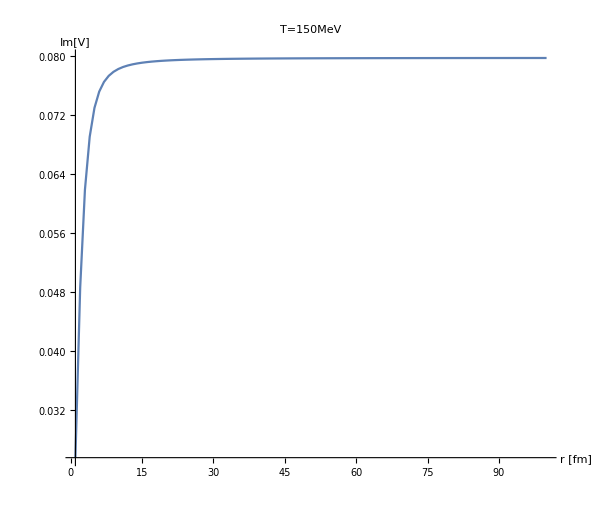

```mathematica
Block[{mD=mDcal[2π,0.155,kfinal[[1]],kfinal[[2]]]},Show[DiscretePlot[ImVc[r/0.197,mD,αcont[[1]],0.155],{r,1,100,1},Joined->True,Filling->None,AxesStyle->Directive[FontSize->25,Thickness->0.004,FontFamily->"Helvetica",Black],BaseStyle->{FontSize->14},PlotRange->All,AspectRatio->0.85,AxesLabel->{"r [fm]","Im[V]"},PlotLabel->Style["T=150MeV",FontSize->25,FontFamily->"Helvetica",Black],ImageSize->{600,600}]]]
```

```mathematica
Series[1/4 mD √π r^3 T σ MeijerG[{{-1/2,-1/2},{}},{{1/2,1/2},{-3/2,-1}},(mD^2 r^2)/4],{r,∞,10}]//FullSimplify
```

ⅇ^(-ⅈ √(-mD^2) r) ((mD T σ (-ⅈ π+Log[-mD^2]-Log[mD^2]) r^2)/(4 √(mD^2))-(3 (mD T σ (π+ⅈ Log[-mD^2]-ⅈ Log[mD^2])) r)/(4 √(-mD^4))+(mD T σ (-ⅈ π+Log[-mD^2]-Log[mD^2]))/((mD^2)^(3/2))+O[1/r]^7)+ⅇ^(ⅈ √(-mD^2) r) ((mD T σ (ⅈ π+Log[-mD^2]-Log[mD^2]) r^2)/(4 √(mD^2))-(3 (mD T σ (π-ⅈ Log[-mD^2]+ⅈ Log[mD^2])) r)/(4 √(-mD^4))+(√(mD^2) T σ (ⅈ π+Log[-mD^2]-Log[mD^2]))/mD^3+O[1/r]^7)+((2 √(mD^2) T σ (-2+2 EulerGamma+Log[mD^2]-2 Log[1/r]))/mD^3-(16 (√(mD^2) T σ))/(mD^5 r^2)-(216 (√(mD^2) T σ))/(mD^7 r^4)-(7680 (√(mD^2) T σ))/(mD^9 r^6)+O[1/r]^8)

```mathematica
ImVsS[r_,mD_,σ_,T_]:=(2 √(mD^2) T σ (-2+2 EulerGamma+Log[mD^2]-2 Log[1/r]))/mD^3-(16 (√(mD^2) T σ))/(mD^5 r^2)-(216 (√(mD^2) T σ))/(mD^7 r^4)-(7680 (√(mD^2) T σ))/(mD^9 r^6)ⅇ^(ⅈ √(-mD^2) r)((mD T σ (ⅈ π+Log[-mD^2]-Log[mD^2]) r^2)/(4 √(mD^2))-(3 (mD T σ (π-ⅈ Log[-mD^2]+ⅈ Log[mD^2])) r)/(4 √(-mD^4))+(√(mD^2) T σ (ⅈ π+Log[-mD^2]-Log[mD^2]))/mD^3)+ⅇ^(-ⅈ √(-mD^2) r)((mD T σ (-ⅈ π+Log[-mD^2]-Log[mD^2]) r^2)/(4 √(mD^2))-(3 (mD T σ (π+ⅈ Log[-mD^2]-ⅈ Log[mD^2])) r)/(4 √(-mD^4))+(mD T σ (-ⅈ π+Log[-mD^2]-Log[mD^2]))/((mD^2)^(3/2)));
```

```mathematica
ImVsS[169,mDcal[2π,0.155,kfinal[[1]],kfinal[[2]]],σcont[[1]],0.155]
```

7.65902-2.14767×10^-18 ⅈ

```mathematica
ImVs[140,mDcal[2π,0.155,kfinal[[1]],kfinal[[2]]],σcont[[1]],0.155]
```

7.64838

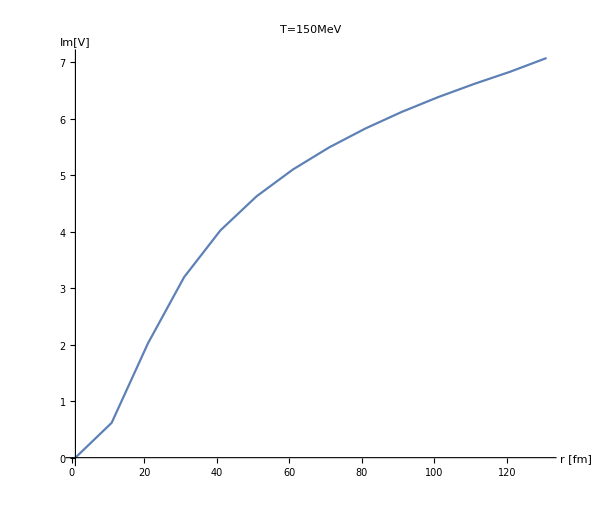

```mathematica
Block[{mD=mDcal[2π,0.155,kfinal[[1]],kfinal[[2]]]},Show[DiscretePlot[ImVs[r,mD,σcont[[1]],0.155],{r,1,140,10},Joined->True,Filling->None,AxesStyle->Directive[FontSize->25,Thickness->0.004,FontFamily->"Helvetica",Black],BaseStyle->{FontSize->14},PlotRange->All,AspectRatio->0.85,AxesLabel->{"r [fm]","Im[V]"},PlotLabel->Style["T=150MeV",FontSize->25,FontFamily->"Helvetica",Black],ImageSize->{600,600}]]]
```

```mathematica
ImVs[20000,mDcal[2π,0.155,kfinal[[1]],kfinal[[2]]],σcont[[1]],0.155]
```

4.5458052209354×10^1789

```mathematica
ImVsS[20000,mDcal[2π,0.155,kfinal[[1]],kfinal[[2]]],σcont[[1]],0.155]
```

19.3543+0. ⅈ

```mathematica
swaveccspectrawsb[n_,Tscan_]:=Block[{T=Tscan[[n]],mD=mDcal[2π,Tscan[[n]],kfinal[[1]],kfinal[[2]]],σ=σcont[[1]],α=αcont[[1]],c=ccont[[1]],M=Mc,l=0,ωmin=-1,ωmax=2,ccsT,Tstring,inf},

rev=Interpolation[Join[ParallelTable[{r,ReV[r,mD,α,σ,c]},{r,1/1000,10,1/100}],ParallelTable[{r,ReV[r,mD,α,σ,c]},{r,101/10,25,1/10}],ParallelTable[{r,ReV[r,mD,α,σ,c]},{r,26,1500,1}],ParallelTable[{r,ReV[r,mD,α,σ,c]},{r,1510,20000,1000}]]];
imv=Interpolation[Join[ParallelTable[{r,ImV[r,mD,α,σ,T]},{r,1/1000,10,1/100}],ParallelTable[{r,ImV[r,mD,α,σ,T]},{r,101/10,25,1/10}],ParallelTable[{r,ImV[r,mD,α,σ,T]},{r,26,140,1}],ParallelTable[{r,ImVc[r,mD,α,T]+ImVsS[r+18,mD,σ,T]},{r,141,1500,1}],ParallelTable[{r,ImVc[r+18,mD,α,T]+ImVsS[r,mD,σ,T]},{r,1510,20000,1000}]]];
V[x_]:=rev[x]+ⅈ imv[x];

ρtable=ParallelDo[ω=ωmin+(it-1) dω M;inf=40+500*it*dω;
(*s0=NDSolve[{(ω-(l(l+1))/(M r^2)-Re[V[r]]+ⅈ Abs[Im[V[r]]])gr[r]+1/M gr''[r]==0, 
gr'[δ]==2 δ(α M)^2-3/4 δ^2(M α)^3,
 gr[δ]== δ^2(α M)^2-1/4 δ^3(M α)^3},gr,{r,δ,inf},PrecisionGoal->10,MaxSteps->1000000];
gr1[r_]=(gr[r]/.s0)_⟦1⟧;*)
s01=NDSolve[{(ω-(l(l+1))/(M r^2)-Re[V[r]]+ⅈ Abs[Im[V[r]]])gr[r]+1/M gr''[r]==0, 
gr'[δ]==(α M)-δ(M α)^2,
 gr[δ]==δ(α M)- 1/2 δ^2(α M)^2},gr,{r,δ,inf}];
gr0[r_]=(gr[r]/.s01)_⟦1⟧;
s1=NDSolve[{rho'[x]==-(6 Nc M^2 α)/(4π)Im[1/(gr0[x])^2(*+36/(gr1[x])^2*)],rho[δ]==0},rho,{x,δ,inf}];
rhow[r_]=(rho[r]/.s1)_⟦1⟧;
ParallelSow[{ω+2M,rhow[inf]}],{it,1,(ωmax-ωmin)/(dω M)}]//Reap//Last//First;

ccsT=ParallelTable[{ρtable[[i,1]],(-ρtable[[i,2]])/ρtable[[i,1]]^2},{i,1,Length[ρtable]}];
Tstring=Round[T*1000];
Export["spectraldata/Tscan/cc/swccT"<>ToString[Tstring]<>"spectrawsb.dat",Sort[ccsT]];
];
```

```mathematica
Tscancorig[[5;;7]]
```

{0.154,0.155,0.156}

```mathematica
Do[swaveccspectrawsb[i,Tscancorig[[5;;7]]],{i,Length[Tscancorig[[5;;7]]]}]//AbsoluteTiming
```

{5173.83,Null}